# Curved rod

This notebook presents ray tracing/quantization results for a shell that’s curved along the x axis.

```mathematica
$Assumptions = _ ∈ Reals;
```

## Ray analysis

```mathematica
H=({{k^4+2 k^2 l^2+l^4+m[x]^2, -ⅈ k m[x], -ⅈ l η m[x]}, {ⅈ k m[x], k^2+1/2 l^2 (1-η), 1/2 k l (1+η)}, {ⅈ l η m[x], 1/2 k l (1+η), l^2+1/2 k^2 (1-η)}});
```

Verify that our expression Λ for the determinant is correct.

```mathematica
Λ=m[x]^2((ω^2-1/2(1-η)l^2)(ω^2-(1-η^2)l^2)-1/2(1-η)k^2 ω^2)-(ω^2-(k^2+l^2)^2)(ω^2-(k^2+l^2))(ω^2-1/2(1-η)(k^2+l^2));
Det[H-ω^2 IdentityMatrix[{3,3}]]-Λ//Simplify
```

3 H ω^4-ω^6+(-k^2-l^2+ω^2) (-(k^2+l^2)^2+ω^2) (1/2 (k^2+l^2) (-1+η)+ω^2)-1/2 (l^4 (-1+η)^2 (1+η)+k^2 (-1+η) ω^2+l^2 (-3+η+2 η^2) ω^2+2 ω^4) m[x]^2

## Quantization

```mathematica
(*  Finds a quantized orbit near another (approximately quantized) 
		orbit by minimizing the estimated quantum number.  *)
quantize[m_, dm_, mInv_, ωGuess_?NumericQ, ϵ_?NumericQ, l:(_?NumericQ):0.1, η:(_?NumericQ):0.3, δ:(_?NumericQ):0.01, OptionsPattern[]] := Module[
	{t, x, k, eqs, sol, caustic, actionIntegral, nEst, ωEst, n, ωRandGuess, res, S},
	
	(*  Location of the caustic on the negative x axis.  *)
	caustic[ω_]:= -mInv[√((ω^2-l^2)/(ω^2-(1-η^2)l^2)(ω^2-l^4))];
	If[OptionValue["Backwards"], S = -1, S = 1];
	
	actionIntegral[ω_] := (
		(*  Set up all equations.  *)
		eqs = {
			x'[t] == S(k[t] (-4 (-1+η) (l^2+k[t]^2)^3+ω^4 (3+4 l^2-η+4 k[t]^2)+ω^2 (l^2+k[t]^2) (3 l^2 (-3+η)+2 (-1+η)+3 (-3+η) k[t]^2)+(-1+η) ω^2 m[x[t]]^2)), 
			k'[t] == -S(((l^2 (-1+η^2)+ω^2) (l^2 (-1+η)+2 ω^2)+(-1+η) ω^2 k[t]^2) m[x[t]] dm[x[t]]),
			k[0] == 0,
			x[0] == caustic[ω],
			
			(*  Ensure that we stop the integration once we reach the turning 
					point on the positive x axis.  We will always start the integration 
					from the turning point on the negative x axis.  *)
			WhenEvent[k[t] == 0 && t > 0, "StopIntegration"]
		};
		
		(*  We should ideally be using a sympletic integrator.  *)
		sol = NDSolve[eqs, {x, k}, {t, 0, ∞}];
		
		(*  Use the undocumented "Domain" method of InterpolatingFunction
				to get the the time at which we hit the next turning point.  *)
		NIntegrate[k[t]D[x[t], t]/.First@sol, {t}~Join~(First@(x/.First@sol)["Domain"])]
	);
	
	(*  Roughly estimate the quantum number n.  *)
	nEst[ωEst_?NumericQ] := actionIntegral[ωEst]/(ϵ π) - 0.5;
	n = Round[nEst[ωGuess]];
	
	If[OptionValue["RandMin"],
		ωRandGuess = RandomReal[{ωGuess - δ, ωGuess + δ}, OptionValue["NRand"]]~Join~{ωGuess};
		res = (nEst[#] - n)^2 & /@ ωRandGuess;
		ωRandGuess = ωRandGuess[[Ordering[res, 1]]][[1]];
		{Round[nEst[ωRandGuess]], ωRandGuess, Min[res]},
		res = NMinimize[(nEst[ωEst] - n)^2, {ωEst, ωGuess - δ, ωGuess + δ}, Method->{"RandomSearch", "SearchPoints"->3}];
		(*  Return as {n, ω, error}.  *)
		{Round@nEst[ωEst/.res[[2]]], ωEst/.res[[2]], res[[1]]}
	]
];

Options[quantize] = {"RandMin"->False, "NRand"->10, "Backwards"->False};
```

```mathematica
√((0.1^2(1-0.3))/2)//N
```

0.0591608

### Examples

#### sech type

```mathematica
m[x_]:=0.1(1-Sech[x]);
dm[x_]:=0.1Sech[x]Tanh[x];
mInv[ω_?NumericQ] := -ArcSech[1-10ω];
```

```mathematica
quantize[m, dm, mInv,0.11108218, 0.01, 0.1, 0.3,0.0001,1,"RandMin"->True]
```

{7,0.111082,0.000111084}

```mathematica
ωSpectral3 = (Transpose@Import["~/code/glwtes/shell/data/sech_bc_cc_l_0.1_eps_0.01_b0.1_N_512/quantized3.txt","Table"])[[1]]
```

{0.10054,0.101872,0.103474,0.105112,0.106747,0.108317,0.109775,0.111082}

```mathematica
Length[ωSpectral2]
```

14

```mathematica
ωQuantize3=ParallelMap[quantize[m, dm, mInv, #, 0.01, 0.1, 0.3,0.005,1]&,ωSpectral3];
```

```mathematica
quantize[m, dm, mInv, 0.033070297, 0.01, 0.1, 0.3,0.005]
```

5.81811

```mathematica
ωQuantize=
```

```mathematica
ωQuantize={{0,0.010856034164611499,1.0286040106553541*^-11},{1,0.013291754944510304,1.7916421012514993*^-14},{2,0.015815372622603508,3.741481141752534*^-15},{3,0.01821508128184155,8.000518901358364*^-17},{4,0.020438240953035734,1.1505790389126477*^-11},{5,0.022471347301050944,1.174195623339054*^-11},{6,0.02431359433732576,3.1037886933889947*^-13},{7,0.025969238676947518,8.387854774044558*^-14},{8,0.027445026174495978,4.0764990373165785*^-16},{9,0.028749295325734704,2.642079405398993*^-12},{10,0.02989160802243336,3.4086857542813464*^-12},{11,0.03088249876511118,6.232458013485096*^-11},{12,0.031733304648634074,4.6918786019396424*^-12},{13,0.03245583985340773,3.2976513722510046*^-11},{14,0.03306215359288343,9.903043242146909*^-16},{15,0.03356415762932548,1.8346892873545682*^-12},{16,0.03397335389481026,1.1713970569435867*^-11},{17,0.03430053991129063,6.409329873770017*^-10},{18,0.0345556274837491,4.0785406196249235*^-10}}
```

{{0,0.010856,1.0286×10^-11},{1,0.0132918,1.79164×10^-14},{2,0.0158154,3.74148×10^-15},{3,0.0182151,8.00052×10^-17},{4,0.0204382,1.15058×10^-11},{5,0.0224713,1.1742×10^-11},{6,0.0243136,3.10379×10^-13},{7,0.0259692,8.38785×10^-14},{8,0.027445,4.0765×10^-16},{9,0.0287493,2.64208×10^-12},{10,0.0298916,3.40869×10^-12},{11,0.0308825,6.23246×10^-11},{12,0.0317333,4.69188×10^-12},{13,0.0324558,3.29765×10^-11},{14,0.0330622,9.90304×10^-16},{15,0.0335642,1.83469×10^-12},{16,0.0339734,1.1714×10^-11},{17,0.0343005,6.40933×10^-10},{18,0.0345556,4.07854×10^-10}}

```mathematica
Export["~/code/glwtes/shell/data/sech_bc_cc_l_0.1_eps_0.01_b0.1_N_512/wkb3.txt",ωQuantize3,"Table"];
```

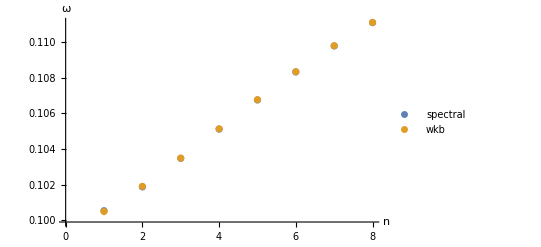

```mathematica
ListPlot[{ωSpectral3,ωQuantize3[[All,2]]},AxesLabel->{"n", "ω"},PlotLegends->{"spectral", "wkb"}]
```

```mathematica
ListPlot[{ωSpectral3,ωQuantize3[[All,2]]},AxesLabel->{"n", "ω"},PlotLegends->{"spectral", "wkb"}]
```

### tanh type

```mathematica
m[x_]:=0.1Tanh[x];
dm[x_]:=0.1 Sech[x]^2;
mInv[ω_?NumericQ] := -ArcTanh[10ω];
```

```mathematica
ωSpectral = (Transpose@Import["~/code/glwtes/shell/data/tanh_bc_cc_l_0.1_eps_0.01_b0.1_N_512/quantized3.txt","Table"])[[1]]
```

{0.101516,0.104807,0.108026,0.11082,0.112924}

```mathematica
Length[ωSpectral1]
```

10

```mathematica
ClearAll[quantize]
```

```mathematica
ωQuantize=ParallelMap[quantize[m, dm, mInv,#, 0.01, 0.1, 0.3,0.0002,"RandMin"->True,"NRand"->300,"Backwards"->True]&, {0.05973787562774366}]
```

{{0,0.0598202,1.62086×10^-10}}

```mathematica
quantize[m, dm, mInv,#, 0.01, 0.1, 0.3,0.0003,"RandMin"->True,"NRand"->300, "Backwards"->False]
```

quantize[m,dm,mInv,#1,0.01,0.1,0.3,0.0003,RandMin→True,NRand→300,Backwards→False]

```mathematica
quantize[m, dm, mInv,0.112723737, 0.01, 0.1, 0.3,0.0002,"RandMin"->True,"NRand"->100, "Backwards"->False]
```

3.86326

$Aborted

```mathematica
Export["wkbx.txt",ωQuantize,"Table"];
```

```mathematica
ωQuantize1=ParallelMap[quantize[m, dm, mInv, #, 0.01, 0.1, 0.3,0.0002,1,"RandMin"->True,"NRand"->300]&,ωSpectral1[[6;;10]]];
```

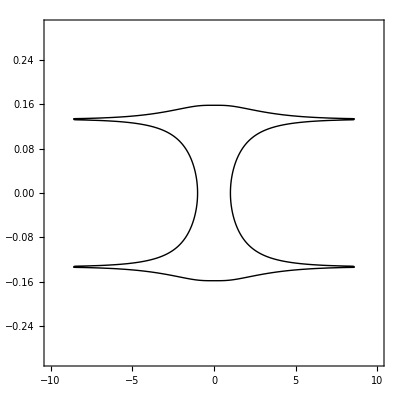

```mathematica
ContourPlot[Λ/.{m[x]->0.1(1-Sech[x]),η->0.3,l->0.1,ω->0.0350241721},{x,-10,10},{k,-0.3,0.3},Contours->{0},ContourShading->None,PlotPoints->200]
```

```mathematica
1/2(l^2+l^4+b^2-√((l^4-l^2+b^2)^2+4 l^2 b^2 η^2))/.{η->0.3,l->0.1,b->0.1}
```

```mathematica
√0.007049583362264501
```

0.0839618

```mathematica
√0.007049583362264501
```

0.0839618

```mathematica
(l^4+η l^2+b^2)^2-((l^4-l^2+b^2)^2+4 η^2 l^2 b^2)//Expand
```

```mathematica
2 b^2 l^2-l^4+2 l^6+2 b^2 l^2 η+2 l^6 η-4 b^2 l^2 η^2+l^4 η^2/.{b->√b}//Simplify
```

```mathematica
Solve[l^4 (1+η) (-1+2 l^2+η)+2 b l^2 (1+η-2 η^2)==0,b]
```

{{b→(l^2 (1+η) (-1+2 l^2+η))/(2 (-1-η+2 η^2))}}

```mathematica
√((l^2 (1+η) (-1+2 l^2+η))/(2 (-1-η+2 η^2)))/.{l->0.1,η->0.3}
```

0.0628206

## Dispersion curves

```mathematica
dispersion[k_,l_,η_,m_]:=Block[{Λ,ω},
Λ=-((-k^2-l^2+ω^2) (-(k^2+l^2)^2+ω^2) (-1/2 (k^2+l^2) (1-η)+ω^2))+m^2 (-1/2 k^2 (1-η) ω^2+(-1/2 l^2 (1-η)+ω^2) (-l^2 (1-η^2)+ω^2));
Select[ω/.Solve[Λ==0,ω], (# > 0)&]
]
```

Find the double well minima: at this ω, for the first time there are 2 real roots.  However, finding this exact ω is impossible with CountRoots, so search for the first point where we have 4 real roots, i.e., slightly above the double well minima.

```mathematica
samples=Table[x,{x, 0.0350241,0.0350243,10^-7/1000}];
samples[[FirstPosition[CountRoots[(Λ/.{η->0.3,m[x]->0.1,l->0.1,ω->#}),k]&/@samples,4][[1]]]]
```

0.0350242

```mathematica
Λ/.{ω->ω[k]}
```

```mathematica
ClearAll["`*"]
```

```mathematica
Λ=-((-k^2-l^2+ω^2) (-(k^2+l^2)^2+ω^2) (-1/2 (k^2+l^2) (1-η)+ω^2))+m^2 (-1/2 k^2 (1-η) ω^2+(-1/2 l^2 (1-η)+ω^2) (-l^2 (1-η^2)+ω^2))/.{m->b}
```

-((-k^2-l^2+ω^2) (-(k^2+l^2)^2+ω^2) (-1/2 (k^2+l^2) (1-η)+ω^2))+b^2 (-1/2 k^2 (1-η) ω^2+(-1/2 l^2 (1-η)+ω^2) (-l^2 (1-η^2)+ω^2))

```mathematica
ω=RandomReal[{0.35,0.36}, 100];
```

```mathematica
ClearAll[doubleWellMin]
```

```mathematica
numRoots[0.1,0.3,0.1,#]&/@ω
```

{16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16}

```mathematica
Clear[ω]
```

```mathematica
0.0350241-0.0350243
```

-2.×10^-7

0.0350242

```mathematica
Ordering[CountRoots[(Λ/.{η->0.3,b->0.1,l->0.1,ω->#}),k]&/@samples,-1]
```

{101}

```mathematica
.
```

```mathematica
0.03502-0.03503
```

-0.00001

```mathematica
Table[ω,{ω, 0.03502,0.03503,0.00001/10}]
```

{0.03502,0.035021,0.035022,0.035023,0.035024,0.035025,0.035026,0.035027,0.035028,0.035029,0.03503}

```mathematica
numRoots[0.1,0.3,0.1,0.03]
```

0

```mathematica
CountRoots[(Λ/.{η->0.3,m[x]->0.1,l->0.1,ω->0.036}),{k,-0.5,0.5}]
```

4

```mathematica
k/.Solve[(Λ/.{η->0.3,b->0.1,l->0.1,ω->0.0365})==0,k]
```

{-0.15583,-0.109894,-0.031667-0.191346 ⅈ,-0.031667+0.191346 ⅈ,0.031667-0.191346 ⅈ,0.031667+0.191346 ⅈ,0.109894,0.15583}

```mathematica
Select[k/.Solve[(Λ/.{η->0.3,b->0.1,l->0.1,ω->0.03502})==0,k], Element[#,Reals] && # > 0&]
```

{}

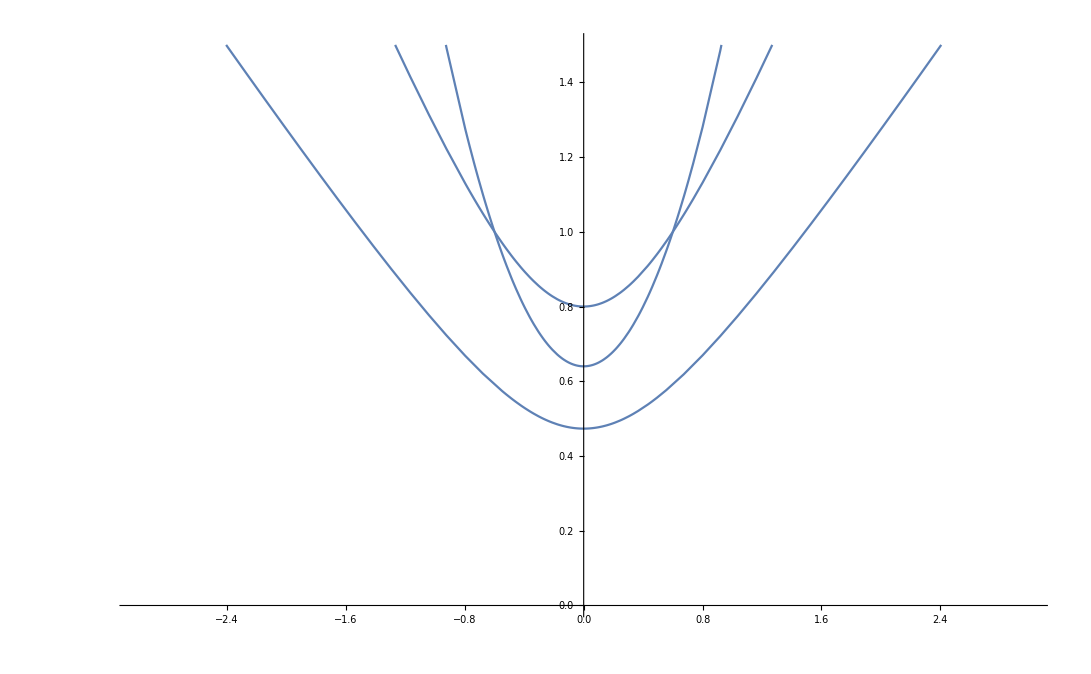

```mathematica
Show[Plot[dispersion[k,0.8,0.3,0],{k,-3,3},PlotRange->{0,1.5}]]
```

```mathematica
-((-0.02600000000000001-k^2) (0.014-0.35 (0.04000000000000001+k^2)) (0.014-(0.04000000000000001+k^2)^2))+100 (3.8857805861880497*^-20-0.0049 k^2) Tanh[x]^2/.{x->0}
```

```mathematica
Solve[-((-0.02600000000000001-k^2) (0.014-0.35 (0.04000000000000001+k^2)) (0.014-(0.04000000000000001+k^2)^2))==0,k]
```

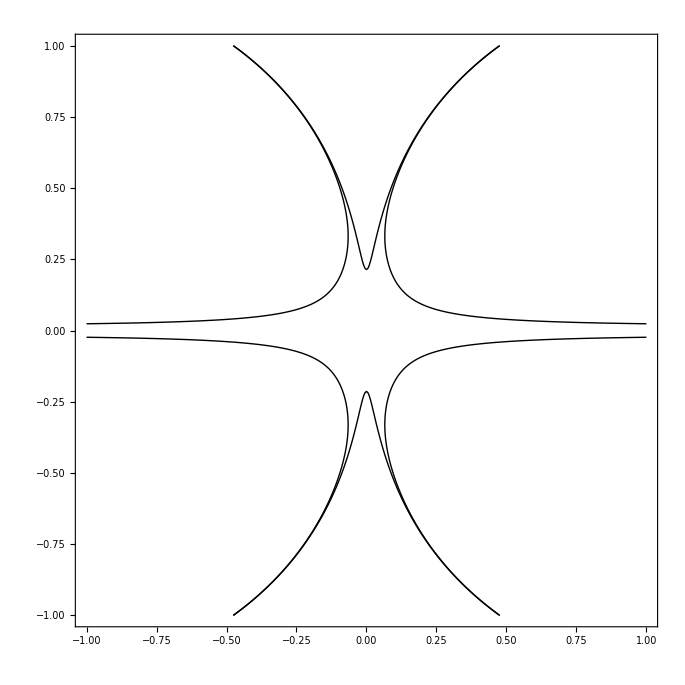

```mathematica
ContourPlot[Λ/.{m[x]->10Tanh[x],l->0.5,η->0.3,ω->√(1/2(1-0.3)0.5^2)},{x,-1,1},{k,-1,1},ContourShading->None,Contours->{0.0,-0.001},PlotPoints->200]
```